## Definitions

```mathematica
ClearAll[h0,x,y,Hz,H,mp,mm];
h0[t_]:=({{0, -t, 0, -t}, {-t, 0, -t, 0}, {0, -t, 0, -t}, {-t, 0, -t, 0}});
x[r0_,J_]:=({{r0, -J, 0, -J}, {-J, 0, J, 0}, {0, J, -r0, J}, {-J, 0, J, 0}});
y[r0_,J_]:=({{0, J, 0, J}, {J, r0, -J, 0}, {0, -J, 0, -J}, {J, 0, -J, -r0}});
Hz[H_]:=H*({{0, 2 I, 0, -2 I}, {-2 I, 0, 2 I, 0}, {0, -2 I, 0, 2 I}, {2 I, 0, -2 I, 0}});
mp[r0_,J_]:=x[r0,J]+I y[r0,J];
mm[r0_,J_]:=x[r0,J]-I y[r0,J];
H[t_,Ox_,Oy_,r0_,J_,q_,U_,h_]:=h0[t]+U*(Ox*x[r0,J]+Oy*y[r0,J])+q*U*(Ox^2+Oy^2)*IdentityMatrix[4]+Hz[h];
```

## Zero Temperature Analysis

### Definitions

```mathematica
(*Quadratic Coefficient*)
α[t_,r0_,J_,q_,U_,h_]:=1/(2!)D[Min[Eigenvalues[H[t,Ox,Oy,r0,J,q,U,h]]],{Ox,2}]/.{Ox->0,Oy->0}
(*Quartic Coefficient*)
β[t_,r0_,J_,q_,U_,h_]:=1/(4!)D[Min[Eigenvalues[H[t,Ox,Oy,r0,J,q,U,h]]],{Ox,4}]/.{Ox->0,Oy->0}
```

### Computations

```mathematica
(* Parameters*)
t:=1
r0:=1
J:=0
q:=.1
OxArr={};
MArr={};
SolArr={};
solThreshhold=10^-6;
αArr={};
βArr={};
Umin :=.01; Umax:=1;Un:=3;dU:=(Umax-Umin)/Un;
hmin:=0;hmax:=1;hn:=3;dh:=(hmax-hmin)/hn;
(*(U,h)Loop *)
Monitor[
Quiet[For[h=hmin,h<hmax,h+=dh,
For[U=Umin,U<Umax,U+=dU,
AppendTo[OxArr,{U,h,FindMinimum[Min[Eigenvalues[H[t,a,b,r0,J,q,U,h]]],{{a,3},{b,0}}][[2]][[1]][[2]],FindMinimum[Min[Eigenvalues[H[t,a,b,r0,J,q,U,h]]],{{a,.1},{b,0}}][[2]][[2]][[2]]}];
AppendTo[MArr,{U,h,Abs[ConjugateTranspose[Eigenvectors[H[t,OxArr[[-1,3]],OxArr[[-1,4]],r0,J,q,U,h]][[1]]].Hz[1].Eigenvectors[H[t,OxArr[[-1,3]],OxArr[[-1,4]],r0,J,q,U,h]][[1]]]}];
AppendTo[αArr,{U,h,α[t,r0,J,q,U,h]}];
AppendTo[βArr,{U,h,β[t,r0,J,q,U,h]}];
If[αArr[[-1]][[3]]<=solThreshhold,AppendTo[SolArr,{U,h}]];
]]];,{"Ox/M Arrays",h,U}]
```

### Plotting

```mathematica
ClearAll[p1,p2,p3,p4,p5,p6,p7]
p1=ListDensityPlot[OxArr[[;;,{1,2,3}]],FrameLabel->{"U","H"},PlotLabel->"<x>"];
p2=ListDensityPlot[MArr[[;;,{1,2,3}]],FrameLabel->{"U","H"},PlotLabel->"M"];
p3=ListLinePlot[SolArr,PlotStyle->{Black,Dashed}];
p4=ListLinePlot[{Select[OxArr,#[[1]]==Umin+dU&][[;;,{2,3}]],Select[MArr,#[[1]]==Umin+dU&][[;;,{2,3}]]},PlotRange->{0,5},AxesLabel->{"H","<x>,M"}];
p5=DensityPlot[Min[Eigenvalues[H[t,Ox,Oy,r0,J,q,U,h]]],{Ox,-5,5},{Oy,-5,5}];
p6=ListDensityPlot[Re[αArr],PlotRange->{-.5,.5},PlotLegends->Automatic,ColorFunction->"TemperatureMap"];
p7=ListDensityPlot[Re[βArr],PlotRange->{-.5,.5},PlotLegends->Automatic,ColorFunction->"TemperatureMap"];
```

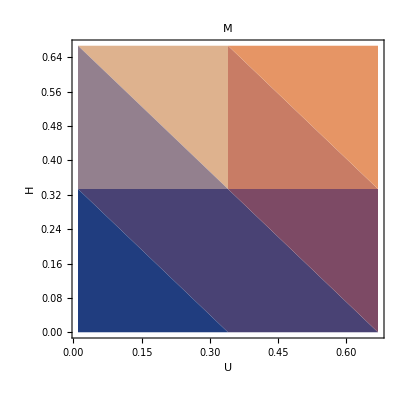

```mathematica
Show[{p2}]
```

## Finite Temperature Analysis

### Definitions

```mathematica
ClearAll[β,t,Ox,Oy,J,q,U,h,Z,F,ψ1,ψ2,ψ3,ψ4,x1,x2,x3,x4,m1,m2,m3,m4,p1,p2,p3,p4,p5,p6,p7,fx,fM,S1,S2,S3,S4]
(* Taylor Expanding Exp[-Uβ (Ox x+Oy y)] w.r.t. Ox, Oy to simplify*)
S1[β_,Ox_,Oy_,r0_,J_,U_]:=-U*β*(Ox *x[r0,J]+Oy*y[r0,J]);
S2[β_,Ox_,Oy_,r0_,J_,U_]:=U^2 β^2(1/(2!)Ox^2 MatrixPower[x[r0,J],2]+1/(1!1!)Ox*Oy*(x[r0,J].y[r0,J]+y[r0,J].x[r0,J])+1/(2!)Oy^2 MatrixPower[y[r0,J],2]);
S3[β_,Ox_,Oy_,r0_,J_,U_]:=-U^3 β^3(1/(3!)Ox^3 MatrixPower[x[r0,J],3]+1/(2!1!)Ox^2 Oy (x[r0,J].x[r0,J].y[r0,J]+x[r0,J].y[r0,J].x[r0,J]+y[r0,J].x[r0,J].x[r0,J])+Ox*Oy^2(y[r0,J].y[r0,J].x[r0,J]+y[r0,J].x[r0,J].y[r0,J]+x[r0,J].y[r0,J].y[r0,J])+1/(3!)Oy^3 MatrixPower[y[r0,J],3]);
S4[β_,Ox_,Oy_,r0_,J_,U_]:=U^4 β^4(1/(4!)Ox^4 MatrixPower[x[r0,J],4]
		+1/(3!1!)Ox^3 Oy(x[r0,J].x[r0,J].x[r0,J].y[r0,J]+x[r0,J].x[r0,J].y[r0,J].x[r0,J]+x[r0,J].y[r0,J].x[r0,J].x[r0,J]+y[r0,J].x[r0,J].x[r0,J].x[r0,J])
		+1/(2!2!)Ox^2 Oy^2(x[r0,J].x[r0,J].y[r0,J].y[r0,J]+x[r0,J].y[r0,J].x[r0,J].y[r0,J]+x[r0,J].y[r0,J].y[r0,J].x[r0,J]+y[r0,J].x[r0,J].x[r0,J].y[r0,J]+y[r0,J].x[r0,J].y[r0,J].x[r0,J]+y[r0,J].y[r0,J].x[r0,J].x[r0,J])
		+1/(1!3!)Ox*Oy^3(y[r0,J].y[r0,J].y[r0,J].x[r0,J]+y[r0,J].y[r0,J].x[r0,J].y[r0,J]+y[r0,J].x[r0,J].y[r0,J].y[r0,J]+x[r0,J].y[r0,J].y[r0,J].y[r0,J])
		+1/(4!)Oy^4 MatrixPower[y[r0,J],4]);
(* Partition Function and Free Energy of Finite Temperature System *)
(*Z[β_,t_,Ox_,Oy_,r0_,J_,q_,U_,h_]:=Tr[MatrixExp[-β*H[t,0,0,r0,J,q,U,h]].(Exp[-β*q*U*(Ox^2+Oy^2)]IdentityMatrix[4]).(IdentityMatrix[4]+S1[β,Ox,Oy,r0,J,U]+S2[β,Ox,Oy,r0,J,U]+S3[β,Ox,Oy,r0,J,U]+S4[β,Ox,Oy,r0,J,U])]*) (*Perturbation theory*)
Z[β_,t_,Ox_,Oy_,r0_,J_,q_,U_,h_]:=Tr[MatrixExp[-β*H[t,Ox,Oy,r0,J,q,U,h]]];
F[β_,t_,Ox_,Oy_,r0_,J_,q_,U_,h_]:=-1/β Log[Z[β,t,Ox,Oy,r0,J,q,U,h]]
(* Eigenstates of Hamiltonian*)
ψ1[t_,Ox_,Oy_,r0_,J_,q_,U_,h_]:=Eigenvectors[H[t,Ox,Oy,r0,J,q,U,h]][[1]]
ψ2[t_,Ox_,Oy_,r0_,J_,q_,U_,h_]:=Eigenvectors[H[t,Ox,Oy,r0,J,q,U,h]][[2]]
ψ3[t_,Ox_,Oy_,r0_,J_,q_,U_,h_]:=Eigenvectors[H[t,Ox,Oy,r0,J,q,U,h]][[3]]
ψ4[t_,Ox_,Oy_,r0_,J_,q_,U_,h_]:=Eigenvectors[H[t,Ox,Oy,r0,J,q,U,h]][[4]]
(*Eigenstate Expectation Values*)
x1[t_,Ox_,Oy_,r0_,J_,q_,U_,h_]:=ConjugateTranspose[ψ1[t,Ox,Oy,r0,J,q,U,h]].x[r0,J].ψ1[t,Ox,Oy,r0,J,q,U,h]
x2[t_,Ox_,Oy_,r0_,J_,q_,U_,h_]:=ConjugateTranspose[ψ2[t,Ox,Oy,r0,J,q,U,h]].x[r0,J].ψ2[t,Ox,Oy,r0,J,q,U,h]
x3[t_,Ox_,Oy_,r0_,J_,q_,U_,h_]:=ConjugateTranspose[ψ3[t,Ox,Oy,r0,J,q,U,h]].x[r0,J].ψ3[t,Ox,Oy,r0,J,q,U,h]
x4[t_,Ox_,Oy_,r0_,J_,q_,U_,h_]:=ConjugateTranspose[ψ4[t,Ox,Oy,r0,J,q,U,h]].x[r0,J].ψ4[t,Ox,Oy,r0,J,q,U,h]
(*Eigenstate Magnetizations*)
m1[t_,Ox_,Oy_,r0_,J_,q_,U_,h_]:=ConjugateTranspose[ψ1[t,Ox,Oy,r0,J,q,U,h]].Hz[1].ψ1[t,Ox,Oy,r0,J,q,U,h]
m2[t_,Ox_,Oy_,r0_,J_,q_,U_,h_]:=ConjugateTranspose[ψ2[t,Ox,Oy,r0,J,q,U,h]].Hz[1].ψ2[t,Ox,Oy,r0,J,q,U,h]
m3[t_,Ox_,Oy_,r0_,J_,q_,U_,h_]:=ConjugateTranspose[ψ3[t,Ox,Oy,r0,J,q,U,h]].Hz[1].ψ3[t,Ox,Oy,r0,J,q,U,h]
m4[t_,Ox_,Oy_,r0_,J_,q_,U_,h_]:=ConjugateTranspose[ψ4[t,Ox,Oy,r0,J,q,U,h]].Hz[1].ψ4[t,Ox,Oy,r0,J,q,U,h]
(*Eigenstate Probabilities*)
p1[β_,t_,Ox_,Oy_,r0_,J_,q_,U_,h_]:=Exp[-β*Eigenvalues[H[t,Ox,Oy,r0,J,q,U,h]][[1]]]/Z[β,t,Ox,Oy,r0,J,q,U,h]
p2[β_,t_,Ox_,Oy_,r0_,J_,q_,U_,h_]:=Exp[-β*Eigenvalues[H[t,Ox,Oy,r0,J,q,U,h]][[2]]]/Z[β,t,Ox,Oy,r0,J,q,U,h]
p3[β_,t_,Ox_,Oy_,r0_,J_,q_,U_,h_]:=Exp[-β*Eigenvalues[H[t,Ox,Oy,r0,J,q,U,h]][[3]]]/Z[β,t,Ox,Oy,r0,J,q,U,h]
p4[β_,t_,Ox_,Oy_,r0_,J_,q_,U_,h_]:=Exp[-β*Eigenvalues[H[t,Ox,Oy,r0,J,q,U,h]][[4]]]/Z[β,t,Ox,Oy,r0,J,q,U,h]
(* Consistency Equation*)
fx[β_,t_,Ox_,Oy_,r0_,J_,q_,U_,h_]:=x1[t,Ox,Oy,r0,J,q,U,h]*p1[β,t,Ox,Oy,r0,J,q,U,h]+x2[t,Ox,Oy,r0,J,q,U,h]*p2[β,t,Ox,Oy,r0,J,q,U,h]+x3[t,Ox,Oy,r0,J,q,U,h]*p3[β,t,Ox,Oy,r0,J,q,U,h]+x4[t,Ox,Oy,r0,J,q,U,h]*p4[β,t,Ox,Oy,r0,J,q,U,h]
(*Magnetization*)
fM[β_,t_,Ox_,Oy_,r0_,J_,q_,U_,h_]:=m1[t,Ox,Oy,r0,J,q,U,h]*p1[β,t,Ox,Oy,r0,J,q,U,h]+m2[t,Ox,Oy,r0,J,q,U,h]*p2[β,t,Ox,Oy,r0,J,q,U,h]+m3[t,Ox,Oy,r0,J,q,U,h]*p3[β,t,Ox,Oy,r0,J,q,U,h]+m4[t,Ox,Oy,r0,J,q,U,h]*p4[β,t,Ox,Oy,r0,J,q,U,h]

(*Quadratic Coefficient of Free Energy *)
αx[β_,t_,r0_,J_,q_,U_,h_]:=1/(2!)Simplify[D[ToRadicals[F[β,t,Ox,Oy,r0,J,q,U,h]],{Ox,2}]/.{Ox->0,Oy->0,h>=0,h<1/4}]
αy[β_,t_,r0_,J_,q_,U_,h_]:=1/(2!)Simplify[D[ToRadicals[F[β,t,Ox,Oy,r0,J,q,U,h]],{Oy,2}]/.{Ox->0,Oy->0}]
(*Quartic Coefficient*)
βxx[β_,t_,r0_,J_,q_,U_,h_]:=1/(4!)Simplify[Simplify[D[ToRadicals[F[β,t,Ox,Oy,r0,J,q,U,h]],{Ox,4}]/.{Ox->0,Oy->0},Assumptions->{h>=0,h<1/4}]]
βxy[β_,t_,r0_,J_,q_,U_,h_]:=1/(4!)Simplify[Simplify[D[ToRadicals[F[β,t,Ox,Oy,r0,J,q,U,h]],{Ox,2},{Oy,2}]/.{Ox->0,Oy->0},Assumptions->{h>=0,h<1/4}]]
βyy[β_,t_,r0_,J_,q_,U_,h_]:=1/(4!)Simplify[Simplify[D[ToRadicals[F[β,t,Ox,Oy,r0,J,q,U,h]],{Oy,4}]/.{Ox->0,Oy->0},Assumptions->{h>=0,h<1/4}]]
(* Magnetic Susceptibility From Second Derivative of α *)
χ[β_,t_,r0_,J_,q_,U_]:=Simplify[Cancel[Simplify[D[αx[β,t,r0,J,q,U,h],{h,2}],Assumptions->{h>=0,h<=1/4}]]/.{h->0}]
(*Magnetic Susceptibility from Full Free Energy *)
χFull[β_,t_,r0_,J_,q_,U_]:=Simplify[Cancel[Simplify[D[F[β,t,Ox,Oy,r0,J,q,U,h],{h,2}]/.{Ox->0,Oy->0}]]]

(* Simplified Versions of Coefficient Functions for faster plotting *)
(* With t = 1, J = 0 *)
(*Quadratic Coefficient of Free Energy *)
Nαx[β_,r0_,q_,U_,h_]:=(U (ⅇ^(4 h β) (4 (-1+4 h^2) q-r0^2 U)+ⅇ^(4 (1+h) β) (4 (-1+4 h^2) q+r0^2 U)+2 ⅇ^(2 β+8 h β) ((-2+8 h^2) q-h r0^2 U)+2 ⅇ^(2 β) ((-2+8 h^2) q+h r0^2 U)))/(2!*2 (ⅇ^(2 β)+ⅇ^(4 h β)+ⅇ^(4 (1+h) β)+ⅇ^(2 β+8 h β)) (-1+4 h^2))
Nαy[β_,r0_,q_,U_,h_]:=(U (ⅇ^(4 h β) (4 (-1+4 h^2) q-r0^2 U)+ⅇ^(4 (1+h) β) (4 (-1+4 h^2) q+r0^2 U)+2 ⅇ^(2 β+8 h β) ((-2+8 h^2) q-h r0^2 U)+2 ⅇ^(2 β) ((-2+8 h^2) q+h r0^2 U)))/(2!*2 (ⅇ^(2 β)+ⅇ^(4 h β)+ⅇ^(4 (1+h) β)+ⅇ^(2 β+8 h β)) (-1+4 h^2))
(*Quartic Coefficients of Free Energy*)
Nβxx[β_,r0_,q_,U_,h_]:=-((3 r0^4 U^4 (2 ⅇ^(4 β) h (3+4 h^2)-2 ⅇ^(4 (β+4 h β)) h (3+4 h^2)-ⅇ^(8 h β) (1+12 h^2)+ⅇ^(8 (1+h) β) (1+12 h^2)+8 ⅇ^(4 β+8 h β) (-1+16 h^4) β+ⅇ^(6 β+4 h β) (1+2 h) (1+h^2 (4-24 β)-2 β+16 h^3 β+4 h (1+3 β))+ⅇ^(6 (β+2 h β)) (-1+2 h) (-1+2 β+16 h^3 β+4 h (1+3 β)+4 h^2 (-1+6 β))+ⅇ^(2 (β+6 h β)) (1+2 h) (-1-2 β+16 h^3 β+4 h (-1+3 β)-4 h^2 (1+6 β))+ⅇ^(2 β+4 h β) (-1+2 h) (1+2 β+16 h^3 β+4 h (-1+3 β)+4 h^2 (1+6 β))))/(4!*8 (ⅇ^(2 β)+ⅇ^(4 h β)+ⅇ^(4 (1+h) β)+ⅇ^(2 β+8 h β))^2 (-1+4 h^2)^3))
Nβxy[β_,r0_,q_,U_,h_]:=-((U^2 (-2 (1-4 h^2)^2 (ⅇ^(4 h β) ((4-16 h^2) q+r0^2 U)-ⅇ^(4 (1+h) β) (4 (-1+4 h^2) q+r0^2 U)-2 ⅇ^(2 β) ((-2+8 h^2) q+h r0^2 U)+ⅇ^(2 β+8 h β) ((4-16 h^2) q+2 h r0^2 U))^2 β+1/h(ⅇ^(2 β)+ⅇ^(4 h β)+ⅇ^(4 (1+h) β)+ⅇ^(2 β+8 h β)) (-1+4 h^2) (ⅇ^(2 β+8 h β) (32 h (-1+4 h^2)^3 q^2 β-32 h^2 (1-4 h^2)^2 q r0^2 U β+r0^4 U^2 (-1+2 h^2-24 h^4-8 h^3 β+32 h^5 β))+ⅇ^(2 β) (32 h (-1+4 h^2)^3 q^2 β+32 h^2 (1-4 h^2)^2 q r0^2 U β+r0^4 U^2 (1-2 h^2+24 h^4-8 h^3 β+32 h^5 β))+ⅇ^(4 (1+h) β) h (32 (-1+4 h^2)^3 q^2 β+16 (1-4 h^2)^2 q r0^2 U β+r0^4 U^2 (3+32 h^4-2 β+h^2 (-4+8 β)))+ⅇ^(4 h β) h (32 (-1+4 h^2)^3 q^2 β-16 (1-4 h^2)^2 q r0^2 U β+r0^4 U^2 (-3-32 h^4-2 β+h^2 (4+8 β))))))/(2!*2!*8 (ⅇ^(2 β)+ⅇ^(4 h β)+ⅇ^(4 (1+h) β)+ⅇ^(2 β+8 h β))^2 (1-4 h^2)^4))
Nβyy[β_,r0_,q_,U_,h_]:=-((3 r0^4 U^4 (2 ⅇ^(4 β) h (3+4 h^2)-2 ⅇ^(4 (β+4 h β)) h (3+4 h^2)-ⅇ^(8 h β) (1+12 h^2)+ⅇ^(8 (1+h) β) (1+12 h^2)+8 ⅇ^(4 β+8 h β) (-1+16 h^4) β+ⅇ^(6 β+4 h β) (1+2 h) (1+h^2 (4-24 β)-2 β+16 h^3 β+4 h (1+3 β))+ⅇ^(6 (β+2 h β)) (-1+2 h) (-1+2 β+16 h^3 β+4 h (1+3 β)+4 h^2 (-1+6 β))+ⅇ^(2 (β+6 h β)) (1+2 h) (-1-2 β+16 h^3 β+4 h (-1+3 β)-4 h^2 (1+6 β))+ⅇ^(2 β+4 h β) (-1+2 h) (1+2 β+16 h^3 β+4 h (-1+3 β)+4 h^2 (1+6 β))))/(4!*8 (ⅇ^(2 β)+ⅇ^(4 h β)+ⅇ^(4 (1+h) β)+ⅇ^(2 β+8 h β))^2 (-1+4 h^2)^3))
(*Magnetic Susceptibility From Second Derivative of α *)
Nχ[β_,r0_,q_,U_]:=-(4 r0^2 U^2 (-1+ⅇ^(6 β)+ⅇ^(4 β) (1-4 β-4 β^2)+ⅇ^(2 β) (-1-4 β+4 β^2)))/(2!*(1+ⅇ^(2 β))^3)
NχFull[β_,r0_,q_,U_,h_]:=-(16 ⅇ^(2 β+4 h β) (1+ⅇ^(4 β)+ⅇ^(8 h β)+4 ⅇ^(2 β+4 h β)+ⅇ^(4 β+8 h β)) β)/((ⅇ^(2 β)+ⅇ^(4 h β)+ⅇ^(4 (1+h) β)+ⅇ^(2 β+8 h β))^2)
(*Taylor Expansion of α in h*)
Taylorα[β_,r0_,q_,U_,h_]:=Nαx[β,q,U,0]+1/2 Nχ[β,r0,q,U]*h^2
```

### Computations

#### Full For Loop (Very slow!!!)

```mathematica
ClearAll[t,r0,J,q,OxArr,MArr,χArr,Umin,Umax,Un,dU,hmin,hmax,hn,dh,Tmin,Tmax,Tn,dT]
(* Parameters *)
t:=1
r0:=1
J:=0
q:=.1
OxArr={};
MArr={};
χArr={};
Umin :=.01; Umax:=1; Un:=32; dU:=(Umax-Umin)/Un;
hmin:=0;hmax:=1; hn:=32; dh:=(hmax-hmin)/hn;
Tmin:=.1;Tmax:=2; Tn:=1; dT:=(Tmax-Tmin)/Tn;
(* For Loop*)
Monitor[
Quiet[For[h=hmin,h<hmax,h+=(hmax-hmin)/hn,
For[U=Umin,U<Umax,U+=(Umax-Umin)/Un,
For[T=Tmin,T<Tmax,T+=(Tmax-Tmin)/Tn,
AppendTo[OxArr,Join[{U,h,T},{a,b}/.FindMinimum[F[1/T,t,a,b,r0,J,q,U,h],{{a,3},{b,0}}][[2]]]];
AppendTo[MArr,{U,h,T,fM[1/T,t,OxArr[[-1]][[4]],OxArr[[-1]][[5]],r0,J,q,U,h]}];
]]]];
,{h,U,T,(Tn*Un*(h-hmin)/dh+Tn*(U-Umin)/dU+(T-Tmin)/dT)/(hn*Un*Tn)}]
```

$Aborted

#### Magnetic Susceptibility For Loop

```mathematica
χArr={};
For[U=Umin,U<Umax,U+=dU,
For[h=hmin,h<hmax,h+=dh,
For[T=Tmin,T<Tmax,T+=dT,
AppendTo[χArr,{U, h, T, (Select[MArr,And[#[[1]]==U,#[[2]]==h+dh,#[[3]]==T]&][[1]][[4]]-Select[MArr,And[#[[1]]==U,#[[2]]==h,#[[3]]==T]&][[1]][[4]])/dh}]
]
]
]
```

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 4 of {}⟦1⟧ does not exist.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
Join[{U,h,T},{a,b}/.FindMinimum[F[1/T,t,a,b,r0,J,q,U,h],{{a,3},{b,0}}][[2]]]
```

{0.690625,1/2,1/10000000000,3.89515,0.}

```mathematica
Re[χArr]
```

#### Solution Set For Loop

```mathematica
(* Parameters *)
t:=1
r0:=1
J:=0
q:=.1
OxArr={};
MArr={};
SolArr={};
TaylorSolArr={};
hmin:=0;hmax:=1; hn:=32; dh:=(hmax-hmin)/hn;
Tmin:=10^-1;Tmax:=2; Tn:=16; dT:=(Tmax-Tmin)/Tn;
(* For Loop*)
Monitor[
Quiet[For[h=hmin,h<hmax,h+=(hmax-hmin)/hn,
For[T=Tmin,T<Tmax,T+=(Tmax-Tmin)/Tn,
AppendTo[SolArr,{U/.NSolve[Nαx[1/T,q,U,h]==0,{U}][[2]],h,T}]; (* Solutions from α = 0*)
AppendTo[TaylorSolArr, {U/.NSolve[Taylorα[1/T,r0,q,U,h]==0,{U}][[2]],h,T}] (*Solutions from Taylor expanded α = 0 *)
]]];
,{h,T}]
```

### Plotting

#### Order Parameter <x> and Magnetization M 3D Plots

```mathematica
ClearAll[plot1,plot2]
plot1=ListDensityPlot3D[OxArr[[;;,{1,2,3,4}]],AxesLabel->{"h","U","T"},PlotLabel->"<x>",PlotRange->All,ColorFunction->"TemperatureMap"];
plot2=ListDensityPlot3D[Re[MArr[[;;,{1,2,3,4}]]],AxesLabel->{"h","U","T"},PlotLabel->"<M>",PlotRange->All,ColorFunction->"TemperatureMap"];
Show[p2]
```

-Graphics3D-

#### Finite Temperature Free Energy Density Plot

```mathematica
t:=1
r0:=1
J:=0
q:=.1
Manipulate[DensityPlot[F[β,t,Ox,Oy,r0,J,q,U,h],{Ox,-5,5},{Oy,-5,5}],{β,.01,2},{U,0,1},{h,0,100}]
```

Visualization`Core`DensityPlot::exclul: {(-0.0492193 Ox^2-0.00901619 Ox^4+0.000180324 Ox^6+8.67362×10^-19 Ox^3 Oy-1.0842×10^-19 Ox^4 Oy-0.0492193 Oy^2-0.0180324 Ox^2 Oy^2+0.000540971 Ox^4 Oy^2+8.67362×10^-19 Ox Oy^3-2.1684×10^-19 Ox^2 Oy^3+«13»)-0,Im[0.25 RootSum[Plus[«48»]&,Times[«2»]&]+0.25 RootSum[Plus[«48»]&,Times[«2»]&]+0.25 RootSum[Plus[«48»]&,Times[«2»]&]+0.25 RootSum[Plus[«48»]&,Times[«2»]&]]-0} must be a list of equalities or real-valued functions.

Visualization`Core`DensityPlot::exclul: {((-3.55271×10^-15-5.55112×10^-16 ⅈ) Ox-(21.3435+2.77556×10^-17 ⅈ) Ox^2-0.00901619 Ox^4+0.000180324 Ox^6-(3.55271×10^-15+2.77556×10^-16 ⅈ) Oy-(21.3435+2.77556×10^-17 ⅈ) Oy^2-0.0180324 Ox^2 Oy^2+0.000540971 Ox^4 Oy^2-0.00901619 Oy^4+0.000540971 Ox^2 Oy^4+«10»)-0,Im[0.25 RootSum[Plus[«38»]&,Times[«2»]&]+0.25 RootSum[Plus[«38»]&,Times[«2»]&]+0.25 RootSum[Plus[«38»]&,Times[«2»]&]+0.25 RootSum[Plus[«38»]&,Times[«2»]&]]-0} must be a list of equalities or real-valued functions.

#### Order Parameter <x> density plot for finite temperature slice T = T_0

$Aborted

$Aborted

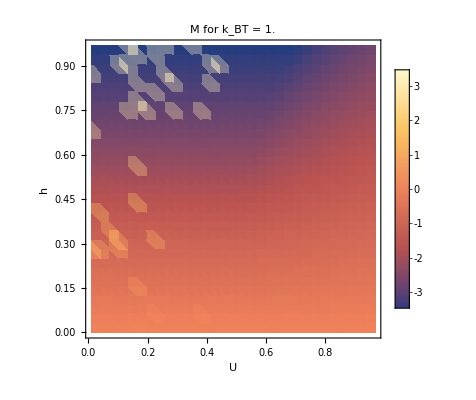

-Graphics-

```mathematica
U0:=Umin+5*dU;
h0:=hmin+20*dh;
T0:=Tmin+0*dT;
plot1=Quiet[ListDensityPlot[Select[OxArr,#[[3]]==T0&][[;;,{1,2,4}]],FrameLabel->{"U", "h"},PlotLabel->"<x> for k_BT = " <>ToString[DecimalForm[N[T0]]],PlotRange->{-1,10}]];
plot2=Quiet[ListDensityPlot[Abs[Select[MArr,#[[3]]==T0&][[;;,{1,2,4}]]],FrameLabel->{"U", "h"},PlotLabel->"M for k_BT = " <>ToString[DecimalForm[N[T0]]],PlotLegends->Automatic]];
plot3=Quiet[ListDensityPlot[Re[Select[χArr,#[[3]]==T0&][[;;,{1,2,4}]]],FrameLabel->{"U", "h"},PlotLabel->"χ for k_BT = " <>ToString[DecimalForm[N[T0]]],PlotLegends->Automatic]];
plot4=Quiet[ListPlot[Re[Select[MArr,(#[[1]]==U0)&&(#[[3]]==T0)&][[;;,{2,4}]]],AxesLabel->{"h","M"},PlotLabel->"M for k_BT = "<>ToString[DecimalForm[N[T0]]]<>", U = "<>ToString[DecimalForm[N[U0]]]]];
plot5=Quiet[ListPlot[Re[Select[MArr,(#[[2]]==h0)&&(#[[3]]==T0)&][[;;,{1,4}]]],AxesLabel->{"U","M"},PlotLabel->"M for k_BT = "<>ToString[DecimalForm[N[T0]]]<>", h = "<>ToString[DecimalForm[N[h0]]]]];
Show[plot2]
Show[plot3]
```

#### Phase Boundary Solutions for Full α=(d^2 F)/(d<x>^2) and Taylor Expanded α^*=α(h=0)+1/2(d^2 α)/dh^2(h=0) *h^2 (t=1,r_0=1,J=0)

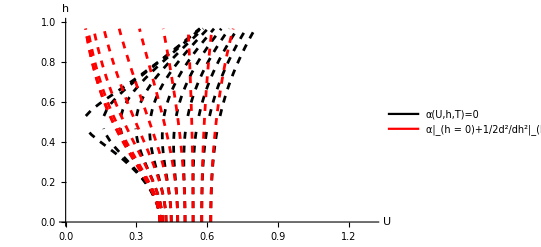

```mathematica
plot1=Quiet[ListLinePlot[Table[Select[SolArr,#[[3]]==Tmin+n*dT&][[;;,{1,2}]],{n,0,10}],PlotStyle->(Table[{Black,Dashed},{i,1,15}]),AxesLabel->{"U","h"},PlotRange->{{0,1.3},{0,1}}]];
plot2=Quiet[ListLinePlot[Table[Select[TaylorSolArr,#[[3]]==Tmin+n*dT&][[;;,{1,2}]],{n,0,10}],PlotStyle->(Table[{Red,Dashed},{i,1,15}]),AxesLabel->{"U","h"},PlotRange->{{0,1.3},{0,1}}]];
Legended[Show[{plot1,plot2}],Placed[LineLegend[{Black,Red},{"α(U,h,T)=0","α|_(h = 0)+1/2d^2/dh^2|_(h = 0)h^2=0"}],{.75,.5}]]
```

#### 2D Quadratic and Quartic Coefficient Plots (t=1,r_0=1,J=0)

```mathematica
Manipulate[Plot[{Nαx[1/T,1,.1,U,h],Nαy[1/T,1,.1,U,h],Nβxx[1/T,1,.1,U,h],Nβxy[1/T,1,.1,U,h],Nβyy[1/T,1,.1,U,h]},{h,10^-5,1},PlotLegends->Placed[{"α_x","α_y","β_xx","β_xy","β_yy"},{1,.5}],AxesLabel->{"h"},PlotRange->{-.1,.1},PlotLabel->StringJoin["T = ",ToString[T],", U = ", ToString[U]]],{T,.1,1},{U,.1,1}]
Manipulate[Plot[{Nαx[1/T,1,.1,U,h],Nαy[1/T,1,.1,U,h],Nβxx[1/T,1,.1,U,h],Nβxy[1/T,1,.1,U,h],Nβyy[1/T,1,.1,U,h]},{U,10^-5,1},PlotLegends->Placed[{"α_x","α_y","β_xx","β_xy","β_yy"},{1,.5}],AxesLabel->{"U"},PlotRange->{-.1,.1},PlotLabel->StringJoin["T = ",ToString[T],", h = ", ToString[h]]],{T,.1,1},{h,.1,1}]
Manipulate[Plot[{Nαx[1/T,1,.1,U,h],Nαy[1/T,1,.1,U,h],Nβxx[1/T,1,.1,U,h],Nβxy[1/T,1,.1,U,h],Nβyy[1/T,1,.1,U,h]},{T,.1,10},PlotLegends->Placed[{"α_x","α_y","β_xx","β_xy","β_yy"},{1,.5}],AxesLabel->{"T"},PlotRange->{-.25,.25},PlotLabel->StringJoin["h = ",ToString[h],", U = ", ToString[U]]],{h,.1,1},{U,.1,1}]
```

```mathematica
ClearAll[r0]
χ[β,1,r0,0,q,U]
Simplify[χFull[β,1,r0,0,q,U],Assumptions->{h>=0,h<1/4}]
```

-(2 r0^2 U^2 (-1+ⅇ^(6 β)+ⅇ^(4 β) (1-4 β-4 β^2)+ⅇ^(2 β) (-1-4 β+4 β^2)))/((1+ⅇ^(2 β))^3)

-(16 ⅇ^(2 β+4 h β) (1+ⅇ^(4 β)+ⅇ^(8 h β)+4 ⅇ^(2 β+4 h β)+ⅇ^(4 β+8 h β)) β)/((ⅇ^(2 β)+ⅇ^(4 h β)+ⅇ^(4 (1+h) β)+ⅇ^(2 β+8 h β))^2)

```mathematica
Simplify[D[F[β,1,Ox,Oy,r0,0,q,U,h],{h,1}],Assumptions->{h>=0,h<1/4}]
```

(8 √2 ⅇ^(-1/2 (6 Ox^2 q U+6 Oy^2 q U+√2 √(4+16 h^2+Ox^2 r0^2 U^2+Oy^2 r0^2 U^2-√(256 h^4+Ox^4 r0^4 U^4+(4+Oy^2 r0^2 U^2)^2+32 h^2 (-4+Ox^2 r0^2 U^2+Oy^2 r0^2 U^2)+Ox^2 (8 r0^2 U^2-2 Oy^2 r0^4 U^4)))+√2 √(4+16 h^2+Ox^2 r0^2 U^2+Oy^2 r0^2 U^2+√(256 h^4+Ox^4 r0^4 U^4+(4+Oy^2 r0^2 U^2)^2+32 h^2 (-4+Ox^2 r0^2 U^2+Oy^2 r0^2 U^2)+Ox^2 (8 r0^2 U^2-2 Oy^2 r0^4 U^4)))) β) h (ⅇ^(2 Ox^2 q U β+2 Oy^2 q U β+(√(4+16 h^2+Ox^2 r0^2 U^2+Oy^2 r0^2 U^2-√(256 h^4+Ox^4 r0^4 U^4+(4+Oy^2 r0^2 U^2)^2+32 h^2 (-4+Ox^2 r0^2 U^2+Oy^2 r0^2 U^2)+Ox^2 (8 r0^2 U^2-2 Oy^2 r0^4 U^4))) β)/(√2)) √(4+16 h^2+Ox^2 r0^2 U^2+Oy^2 r0^2 U^2-√(256 h^4+Ox^4 r0^4 U^4+(4+Oy^2 r0^2 U^2)^2+32 h^2 (-4+Ox^2 r0^2 U^2+Oy^2 r0^2 U^2)+Ox^2 (8 r0^2 U^2-2 Oy^2 r0^4 U^4))) (-4+16 h^2+Ox^2 r0^2 U^2+Oy^2 r0^2 U^2+√(256 h^4+Ox^4 r0^4 U^4+(4+Oy^2 r0^2 U^2)^2+32 h^2 (-4+Ox^2 r0^2 U^2+Oy^2 r0^2 U^2)+Ox^2 (8 r0^2 U^2-2 Oy^2 r0^4 U^4)))-ⅇ^(2 Ox^2 q U β+2 Oy^2 q U β+(√(4+16 h^2+Ox^2 r0^2 U^2+Oy^2 r0^2 U^2-√(256 h^4+Ox^4 r0^4 U^4+(4+Oy^2 r0^2 U^2)^2+32 h^2 (-4+Ox^2 r0^2 U^2+Oy^2 r0^2 U^2)+Ox^2 (8 r0^2 U^2-2 Oy^2 r0^4 U^4))) β)/(√2)+√2 √(4+16 h^2+Ox^2 r0^2 U^2+Oy^2 r0^2 U^2+√(256 h^4+Ox^4 r0^4 U^4+(4+Oy^2 r0^2 U^2)^2+32 h^2 (-4+Ox^2 r0^2 U^2+Oy^2 r0^2 U^2)+Ox^2 (8 r0^2 U^2-2 Oy^2 r0^4 U^4))) β) √(4+16 h^2+Ox^2 r0^2 U^2+Oy^2 r0^2 U^2-√(256 h^4+Ox^4 r0^4 U^4+(4+Oy^2 r0^2 U^2)^2+32 h^2 (-4+Ox^2 r0^2 U^2+Oy^2 r0^2 U^2)+Ox^2 (8 r0^2 U^2-2 Oy^2 r0^4 U^4))) (-4+16 h^2+Ox^2 r0^2 U^2+Oy^2 r0^2 U^2+√(256 h^4+Ox^4 r0^4 U^4+(4+Oy^2 r0^2 U^2)^2+32 h^2 (-4+Ox^2 r0^2 U^2+Oy^2 r0^2 U^2)+Ox^2 (8 r0^2 U^2-2 Oy^2 r0^4 U^4)))+ⅇ^(2 Ox^2 q U β+2 Oy^2 q U β+√2 √(4+16 h^2+Ox^2 r0^2 U^2+Oy^2 r0^2 U^2-√(256 h^4+Ox^4 r0^4 U^4+(4+Oy^2 r0^2 U^2)^2+32 h^2 (-4+Ox^2 r0^2 U^2+Oy^2 r0^2 U^2)+Ox^2 (8 r0^2 U^2-2 Oy^2 r0^4 U^4))) β+(√(4+16 h^2+Ox^2 r0^2 U^2+Oy^2 r0^2 U^2+√(256 h^4+Ox^4 r0^4 U^4+(4+Oy^2 r0^2 U^2)^2+32 h^2 (-4+Ox^2 r0^2 U^2+Oy^2 r0^2 U^2)+Ox^2 (8 r0^2 U^2-2 Oy^2 r0^4 U^4))) β)/(√2)) (-4+16 h^2+Ox^2 r0^2 U^2+Oy^2 r0^2 U^2-√(256 h^4+Ox^4 r0^4 U^4+(4+Oy^2 r0^2 U^2)^2+32 h^2 (-4+Ox^2 r0^2 U^2+Oy^2 r0^2 U^2)+Ox^2 (8 r0^2 U^2-2 Oy^2 r0^4 U^4))) √(4+16 h^2+Ox^2 r0^2 U^2+Oy^2 r0^2 U^2+√(256 h^4+Ox^4 r0^4 U^4+(4+Oy^2 r0^2 U^2)^2+32 h^2 (-4+Ox^2 r0^2 U^2+Oy^2 r0^2 U^2)+Ox^2 (8 r0^2 U^2-2 Oy^2 r0^4 U^4)))+ⅇ^(2 Ox^2 q U β+2 Oy^2 q U β+(√(4+16 h^2+Ox^2 r0^2 U^2+Oy^2 r0^2 U^2+√(256 h^4+Ox^4 r0^4 U^4+(4+Oy^2 r0^2 U^2)^2+32 h^2 (-4+Ox^2 r0^2 U^2+Oy^2 r0^2 U^2)+Ox^2 (8 r0^2 U^2-2 Oy^2 r0^4 U^4))) β)/(√2)) (4-16 h^2-Ox^2 r0^2 U^2-Oy^2 r0^2 U^2+√(256 h^4+Ox^4 r0^4 U^4+(4+Oy^2 r0^2 U^2)^2+32 h^2 (-4+Ox^2 r0^2 U^2+Oy^2 r0^2 U^2)+Ox^2 (8 r0^2 U^2-2 Oy^2 r0^4 U^4))) √(4+16 h^2+Ox^2 r0^2 U^2+Oy^2 r0^2 U^2+√(256 h^4+Ox^4 r0^4 U^4+(4+Oy^2 r0^2 U^2)^2+32 h^2 (-4+Ox^2 r0^2 U^2+Oy^2 r0^2 U^2)+Ox^2 (8 r0^2 U^2-2 Oy^2 r0^4 U^4)))))/((ⅇ^(-1/2 (2 Ox^2 q U+2 Oy^2 q U+√2 √(4+16 h^2+Ox^2 r0^2 U^2+Oy^2 r0^2 U^2-√(256 h^4+Ox^4 r0^4 U^4+(4+Oy^2 r0^2 U^2)^2+32 h^2 (-4+Ox^2 r0^2 U^2+Oy^2 r0^2 U^2)+Ox^2 (8 r0^2 U^2-2 Oy^2 r0^4 U^4)))) β)+ⅇ^(-1/2 (2 Ox^2 q U+2 Oy^2 q U+√2 √(4+16 h^2+Ox^2 r0^2 U^2+Oy^2 r0^2 U^2+√(256 h^4+Ox^4 r0^4 U^4+(4+Oy^2 r0^2 U^2)^2+32 h^2 (-4+Ox^2 r0^2 U^2+Oy^2 r0^2 U^2)+Ox^2 (8 r0^2 U^2-2 Oy^2 r0^4 U^4)))) β)+ⅇ^(-Ox^2 q U β-Oy^2 q U β+(√(4+16 h^2+Ox^2 r0^2 U^2+Oy^2 r0^2 U^2-√(256 h^4+Ox^4 r0^4 U^4+(4+Oy^2 r0^2 U^2)^2+32 h^2 (-4+Ox^2 r0^2 U^2+Oy^2 r0^2 U^2)+Ox^2 (8 r0^2 U^2-2 Oy^2 r0^4 U^4))) β)/(√2))+ⅇ^(-Ox^2 q U β-Oy^2 q U β+(√(4+16 h^2+Ox^2 r0^2 U^2+Oy^2 r0^2 U^2+√(256 h^4+Ox^4 r0^4 U^4+(4+Oy^2 r0^2 U^2)^2+32 h^2 (-4+Ox^2 r0^2 U^2+Oy^2 r0^2 U^2)+Ox^2 (8 r0^2 U^2-2 Oy^2 r0^4 U^4))) β)/(√2))) √(256 h^4+Ox^4 r0^4 U^4+(4+Oy^2 r0^2 U^2)^2+32 h^2 (-4+Ox^2 r0^2 U^2+Oy^2 r0^2 U^2)+Ox^2 (8 r0^2 U^2-2 Oy^2 r0^4 U^4)) √(4+16 h^2+Ox^2 r0^2 U^2+Oy^2 r0^2 U^2-√(256 h^4+Ox^4 r0^4 U^4+(4+Oy^2 r0^2 U^2)^2+32 h^2 (-4+Ox^2 r0^2 U^2+Oy^2 r0^2 U^2)+Ox^2 (8 r0^2 U^2-2 Oy^2 r0^4 U^4))) √(4+16 h^2+Ox^2 r0^2 U^2+Oy^2 r0^2 U^2+√(256 h^4+Ox^4 r0^4 U^4+(4+Oy^2 r0^2 U^2)^2+32 h^2 (-4+Ox^2 r0^2 U^2+Oy^2 r0^2 U^2)+Ox^2 (8 r0^2 U^2-2 Oy^2 r0^4 U^4))))

```mathematica
%/.{h->0}
```

-(16 ⅇ^(2 β) (2+4 ⅇ^(2 β)+2 ⅇ^(4 β)) β)/((1+2 ⅇ^(2 β)+ⅇ^(4 β))^2)

```mathematica
F[β,1,Ox,Oy,r0,0,q,U,h]/.{Ox->0,Oy->0}
```

```mathematica
-1/β Log[-(2 √2 ⅇ^(-(√(4+16 h^2+√(16-128 h^2+256 h^4)) β)/(√2)) √(4+16 h^2+√(16-128 h^2+256 h^4)) (2 (1-2 ⅈ h) (1+2 ⅈ h)+1/2 (-4-16 h^2+√(16-128 h^2+256 h^4))))/(-((-8-32 h^2) √(4+16 h^2+√(16-128 h^2+256 h^4)))/(√2)-√2 (4+16 h^2+√(16-128 h^2+256 h^4))^(3/2))+(2 √2 ⅇ^((√(4+16 h^2+√(16-128 h^2+256 h^4)) β)/(√2)) √(4+16 h^2+√(16-128 h^2+256 h^4)) (2 (1-2 ⅈ h) (1+2 ⅈ h)+1/2 (-4-16 h^2+√(16-128 h^2+256 h^4))))/(((-8-32 h^2) √(4+16 h^2+√(16-128 h^2+256 h^4)))/(√2)+√2 (4+16 h^2+√(16-128 h^2+256 h^4))^(3/2))+(4 ⅇ^(-(√(4+16 h^2-√(16-128 h^2+256 h^4)) β)/(√2)) ((1+2 ⅈ h) (-((1-2 ⅈ h) √(4+16 h^2-√(16-128 h^2+256 h^4)))/(√2)+((1-2 ⅈ h) √(4+16 h^2+√(16-128 h^2+256 h^4)))/(√2))+(1-2 ⅈ h) (-((1+2 ⅈ h) √(4+16 h^2-√(16-128 h^2+256 h^4)))/(√2)+((1+2 ⅈ h) √(4+16 h^2+√(16-128 h^2+256 h^4)))/(√2))-(√(4+16 h^2+√(16-128 h^2+256 h^4)) (2 (1-2 ⅈ h) (1+2 ⅈ h)-1/2 √(4+16 h^2-√(16-128 h^2+256 h^4)) √(4+16 h^2+√(16-128 h^2+256 h^4))))/(√2)))/(-((-8-32 h^2) √(4+16 h^2-√(16-128 h^2+256 h^4)))/(√2)-√2 (4+16 h^2-√(16-128 h^2+256 h^4))^(3/2))+(4 ⅇ^((√(4+16 h^2-√(16-128 h^2+256 h^4)) β)/(√2)) ((1+2 ⅈ h) (((1-2 ⅈ h) √(4+16 h^2-√(16-128 h^2+256 h^4)))/(√2)+((1-2 ⅈ h) √(4+16 h^2+√(16-128 h^2+256 h^4)))/(√2))+(1-2 ⅈ h) (((1+2 ⅈ h) √(4+16 h^2-√(16-128 h^2+256 h^4)))/(√2)+((1+2 ⅈ h) √(4+16 h^2+√(16-128 h^2+256 h^4)))/(√2))-(√(4+16 h^2+√(16-128 h^2+256 h^4)) (2 (1-2 ⅈ h) (1+2 ⅈ h)+1/2 √(4+16 h^2-√(16-128 h^2+256 h^4)) √(4+16 h^2+√(16-128 h^2+256 h^4))))/(√2)))/(((-8-32 h^2) √(4+16 h^2-√(16-128 h^2+256 h^4)))/(√2)+√2 (4+16 h^2-√(16-128 h^2+256 h^4))^(3/2))]
```

```mathematica
ClearAll[β,r0,q,U,h]
Simplify[Limit[Nβxy[β,r0,q,U,h],β->0]]
```

0

```mathematica
Simplify[-(16 ⅇ^(2 β) (2+4 ⅇ^(2 β)+2 ⅇ^(4 β)) β)/((1+2 ⅇ^(2 β)+ⅇ^(4 β))^2)]
```

-(32 ⅇ^(2 β) β)/((1+ⅇ^(2 β))^2)

```mathematica
Cancel[%609]
```

1/(192 (ⅇ^(2 β)+ⅇ^(4 h β)+ⅇ^(4 (1+h) β)+ⅇ^(2 β+8 h β))^2 h (-1+4 h^2)^3)U^4 (-ⅇ^(4 β) r0^4-ⅇ^(2 β+4 h β) r0^4+ⅇ^(2 β+12 h β) r0^4+ⅇ^(4 β+16 h β) r0^4-ⅇ^(2 β+4 (1+h) β) r0^4+ⅇ^(2 β+8 h β+4 (1+h) β) r0^4+3 ⅇ^(8 h β) h r0^4-3 ⅇ^(8 (1+h) β) h r0^4+3 ⅇ^(2 β+4 h β) h r0^4+3 ⅇ^(2 β+12 h β) h r0^4-3 ⅇ^(2 β+4 (1+h) β) h r0^4-3 ⅇ^(2 β+8 h β+4 (1+h) β) h r0^4+2 ⅇ^(4 β) h^2 r0^4+2 ⅇ^(2 β+4 h β) h^2 r0^4-2 ⅇ^(2 β+12 h β) h^2 r0^4-2 ⅇ^(4 β+16 h β) h^2 r0^4+2 ⅇ^(2 β+4 (1+h) β) h^2 r0^4-2 ⅇ^(2 β+8 h β+4 (1+h) β) h^2 r0^4-4 ⅇ^(8 h β) h^3 r0^4+4 ⅇ^(8 (1+h) β) h^3 r0^4-4 ⅇ^(2 β+4 h β) h^3 r0^4-4 ⅇ^(2 β+12 h β) h^3 r0^4+4 ⅇ^(2 β+4 (1+h) β) h^3 r0^4+4 ⅇ^(2 β+8 h β+4 (1+h) β) h^3 r0^4-24 ⅇ^(4 β) h^4 r0^4-24 ⅇ^(2 β+4 h β) h^4 r0^4+24 ⅇ^(2 β+12 h β) h^4 r0^4+24 ⅇ^(4 β+16 h β) h^4 r0^4-24 ⅇ^(2 β+4 (1+h) β) h^4 r0^4+24 ⅇ^(2 β+8 h β+4 (1+h) β) h^4 r0^4+32 ⅇ^(8 h β) h^5 r0^4-32 ⅇ^(8 (1+h) β) h^5 r0^4+32 ⅇ^(2 β+4 h β) h^5 r0^4+32 ⅇ^(2 β+12 h β) h^5 r0^4-32 ⅇ^(2 β+4 (1+h) β) h^5 r0^4-32 ⅇ^(2 β+8 h β+4 (1+h) β) h^5 r0^4+2 ⅇ^(2 β+4 h β) h r0^4 β+2 ⅇ^(2 β+12 h β) h r0^4 β+2 ⅇ^(2 β+4 (1+h) β) h r0^4 β+8 ⅇ^(4 h β+4 (1+h) β) h r0^4 β+2 ⅇ^(2 β+8 h β+4 (1+h) β) h r0^4 β+8 ⅇ^(2 β+4 h β) h^2 r0^4 β-8 ⅇ^(2 β+12 h β) h^2 r0^4 β-8 ⅇ^(2 β+4 (1+h) β) h^2 r0^4 β+8 ⅇ^(2 β+8 h β+4 (1+h) β) h^2 r0^4 β+32 ⅇ^(4 β+8 h β) h^3 r0^4 β-32 ⅇ^(4 h β+4 (1+h) β) h^3 r0^4 β-32 ⅇ^(2 β+4 h β) h^4 r0^4 β+32 ⅇ^(2 β+12 h β) h^4 r0^4 β+32 ⅇ^(2 β+4 (1+h) β) h^4 r0^4 β-32 ⅇ^(2 β+8 h β+4 (1+h) β) h^4 r0^4 β-32 ⅇ^(2 β+4 h β) h^5 r0^4 β-128 ⅇ^(4 β+8 h β) h^5 r0^4 β-32 ⅇ^(2 β+12 h β) h^5 r0^4 β-32 ⅇ^(2 β+4 (1+h) β) h^5 r0^4 β-32 ⅇ^(2 β+8 h β+4 (1+h) β) h^5 r0^4 β)

```mathematica
Simplify[-(U^2 (-2 (1-4 h^2)^2 (ⅇ^(4 h β) ((4-16 h^2) q+r0^2 U)-ⅇ^(4 (1+h) β) (4 (-1+4 h^2) q+r0^2 U)-2 ⅇ^(2 β) ((-2+8 h^2) q+h r0^2 U)+ⅇ^(2 β+8 h β) ((4-16 h^2) q+2 h r0^2 U))^2 β+((ⅇ^(2 β)+ⅇ^(4 h β)+ⅇ^(4 (1+h) β)+ⅇ^(2 β+8 h β)) (-1+4 h^2) (ⅇ^(2 β+8 h β) (32 h (-1+4 h^2)^3 q^2 β-32 h^2 (1-4 h^2)^2 q r0^2 U β+r0^4 U^2 (-1+2 h^2-24 h^4-8 h^3 β+32 h^5 β))+ⅇ^(2 β) (32 h (-1+4 h^2)^3 q^2 β+32 h^2 (1-4 h^2)^2 q r0^2 U β+r0^4 U^2 (1-2 h^2+24 h^4-8 h^3 β+32 h^5 β))+ⅇ^(4 (1+h) β) h (32 (-1+4 h^2)^3 q^2 β+16 (1-4 h^2)^2 q r0^2 U β+r0^4 U^2 (3+32 h^4-2 β+h^2 (-4+8 β)))+ⅇ^(4 h β) h (32 (-1+4 h^2)^3 q^2 β-16 (1-4 h^2)^2 q r0^2 U β+r0^4 U^2 (-3-32 h^4-2 β+h^2 (4+8 β)))))/h))/(8 (ⅇ^(2 β)+ⅇ^(4 h β)+ⅇ^(4 (1+h) β)+ⅇ^(2 β+8 h β))^2 (1-4 h^2)^4)==-(r0^4 U^4 (ⅇ^(4 (β+4 h β)) (-1+2 h^2-24 h^4)+ⅇ^(4 β) (1-2 h^2+24 h^4)-ⅇ^(8 h β) h (3-4 h^2+32 h^4)+ⅇ^(8 (1+h) β) h (3-4 h^2+32 h^4)+8 ⅇ^(4 β+8 h β) h (-1+16 h^4) β+ⅇ^(6 β+4 h β) (1+2 h) (1+h+h^3 (4-24 β)-2 h β+16 h^4 (1+β)+4 h^2 (-1+3 β))+ⅇ^(6 (1+2 h) β) (-1+2 h) (1+16 h^4 (1+β)+h (-1+2 β)+4 h^2 (-1+3 β)+4 h^3 (-1+6 β))+ⅇ^(2 (β+6 h β)) (1+2 h) (-1+16 h^4 (-1+β)-h (1+2 β)+4 h^2 (1+3 β)-4 h^3 (1+6 β))+ⅇ^(2 β+4 h β) (-1+2 h) (-1+h+16 h^4 (-1+β)+2 h β+4 h^2 (1+3 β)+4 h^3 (1+6 β))))/(8 (ⅇ^(2 β)+ⅇ^(4 h β)+ⅇ^(4 (1+h) β)+ⅇ^(2 β+8 h β))^2 h (-1+4 h^2)^3)]
```

True